## Author: Sreenath K. Manikandan, Nordita, KTH Royal Institute of Technology and Stockholm University

## Steady state of the clock: full model

```mathematica
Clear[H0,r0,Ω ,ω,gamma,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
rhee={{as,es+I fs,cs+I ds},{es-I fs,bs,gs+ I hs},{cs-I ds,gs-I hs,1-as-bs}};oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];gw=.;as=.;bs=.;g0=.;gamma=.;gammah=.;gammac=.;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];Lw=KroneckerProduct[{{0},{1},{0}},{1,0,0}];Lwd=KroneckerProduct[{{1},{0},{0}},{0,1,0}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
Ω =.;ω =.;dt=.;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
```

```mathematica
FullSimplify[Solve[1/dt(dt (-I (H0.rhee-rhee.H0)-gamma (oX.(oX.rhee-rhee.oX)-(oX.rhee-rhee.oX).oX)+gammah(Lh.rhee.Lhd-1/2(rhee.Lhd.Lh+Lhd.Lh.rhee))+gammah Exp[-betah Ω ](Lhd.rhee.Lh-1/2(rhee.Lh.Lhd+Lh.Lhd.rhee))+gammac(Lc.rhee.Lcd-1/2(rhee.Lcd.Lc+Lcd.Lc.rhee))+gammac Exp[-betac ω ](Lcd.rhee.Lc-1/2(rhee.Lc.Lcd+Lc.Lcd.rhee))+gw(Lw.rhee.Lwd-1/2(rhee.Lwd.Lw+Lwd.Lw.rhee))))=={{0,0,0},{0,0,0},{0,0,0}},{as,bs,cs,ds,es,fs,gs,hs}],Assumptions->{gamma>0,gammac>0,gammah>0,as>0,bs>0}]
```

```mathematica
ast=-((ⅇ^(betac ω) gammac (-ⅇ^(2 betac ω) gammah^3-ⅇ^(betac ω+betah Ω) gammah^2 (2 gammac+ⅇ^(betac ω) (13 gamma+2 (gammah+gw)))+ⅇ^(3 betah Ω) gamma (-gammac^2-2 ⅇ^(betac ω) gammac (4 gamma+gammah+gw)-ⅇ^(2 betac ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))+ⅇ^(2 betah Ω) gammah (-gammac^2-2 ⅇ^(betac ω) gammac (7 gamma+gammah+gw)-ⅇ^(2 betac ω) ((4 gamma+gammah+gw) (10 gamma+gammah+gw)+4 Ω^2))+ⅇ^(betah Ω) gamma (ⅇ^(2 betah Ω) gammac^2+2 ⅇ^(betac ω+betah Ω) gammac (-gammah+ⅇ^(betah Ω) (4 gamma+gammah+gw))+ⅇ^(2 betac ω) (-3 gammah^2-2 ⅇ^(betah Ω) gammah (12 gamma+gammah+gw)+ⅇ^(2 betah Ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))) Cos[2 theta]))/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta]));bst=-((-ⅇ^(3 betac ω) gammah^3 gw-ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+gammah+3 gw)+ⅇ^(betac ω) gw (13 gamma+2 (gammah+gw)))-ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 (gamma+gammah)+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+7 gamma (gammah+2 gw)+(gammah+gw) (gammah+2 gw))+ⅇ^(2 betac ω) gw ((4 gamma+gammah+gw) (10 gamma+gammah+gw)+4 Ω^2))+ⅇ^(3 betah Ω) (-gammac^3 (gamma+gammah+gw)-ⅇ^(betac ω) gammac^2 (8 gamma^2+2 (gammah+gw)^2+gamma (14 gammah+15 gw))-ⅇ^(3 betac ω) gamma gw ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2)-ⅇ^(2 betac ω) gammac ((gammah+gw)^3+8 gamma^2 (5 gammah+6 gw)+gamma (gammah+gw) (13 gammah+15 gw)+4 gamma Ω^2+4 (gammah+gw) Ω^2))+ⅇ^(betah Ω) gamma (ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (2 gammah-ⅇ^(betah Ω) (-8 gamma+2 gammah+gw))+ⅇ^(2 betac ω) gammac (gammah^2-2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)-ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) gw (-3 gammah^2-2 ⅇ^(betah Ω) gammah (12 gamma+gammah+gw)+ⅇ^(2 betah Ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))) Cos[2 theta])/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta]));cst=-((2 ⅇ^(-ⅈ phi+2 betac ω+betah Ω) gamma gammac (-gammah+ⅇ^(betah Ω) (gammah+gw)) (ⅇ^(betah Ω) gammac+ⅇ^(2 ⅈ phi+betah Ω) gammac+ⅇ^(betac ω) gammah+ⅇ^(2 ⅈ phi+betac ω) gammah+ⅇ^(2 ⅈ phi+betac ω+betah Ω) (8 gamma+gammah+gw-2 ⅈ Ω)+ⅇ^(betac ω+betah Ω) (8 gamma+gammah+gw+2 ⅈ Ω)) Cos[theta] Sin[theta])/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta]));dst=(2 ⅈ ⅇ^(-ⅈ phi+2 betac ω+betah Ω) gamma gammac (-gammah+ⅇ^(betah Ω) (gammah+gw)) (-ⅇ^(betah Ω) gammac+ⅇ^(2 ⅈ phi+betah Ω) gammac-ⅇ^(betac ω) gammah+ⅇ^(2 ⅈ phi+betac ω) gammah+ⅇ^(2 ⅈ phi+betac ω+betah Ω) (8 gamma+gammah+gw-2 ⅈ Ω)-ⅇ^(betac ω+betah Ω) (8 gamma+gammah+gw+2 ⅈ Ω)) Cos[theta] Sin[theta])/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta]);est=0;fst=0;gst=0;hst=0;
```

```mathematica
{{ast,est+I fst,cst+I dst},{est-I fst,bst,gst+ I hst},{cst-I dst,gst-I hst,1-ast-bst}};
```

```mathematica
rst[theta_,phi_,betah_,betac_,gamma_,gammac_,gammah_,gw_,Ω_,ω_]:={{-((ⅇ^(betac ω) gammac (-ⅇ^(2 betac ω) gammah^3-ⅇ^(betac ω+betah Ω) gammah^2 (2 gammac+ⅇ^(betac ω) (13 gamma+2 (gammah+gw)))+ⅇ^(3 betah Ω) gamma (-gammac^2-2 ⅇ^(betac ω) gammac (4 gamma+gammah+gw)-ⅇ^(2 betac ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))+ⅇ^(2 betah Ω) gammah (-gammac^2-2 ⅇ^(betac ω) gammac (7 gamma+gammah+gw)-ⅇ^(2 betac ω) ((4 gamma+gammah+gw) (10 gamma+gammah+gw)+4 Ω^2))+ⅇ^(betah Ω) gamma (ⅇ^(2 betah Ω) gammac^2+2 ⅇ^(betac ω+betah Ω) gammac (-gammah+ⅇ^(betah Ω) (4 gamma+gammah+gw))+ⅇ^(2 betac ω) (-3 gammah^2-2 ⅇ^(betah Ω) gammah (12 gamma+gammah+gw)+ⅇ^(2 betah Ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))) Cos[2 theta]))/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta])),0,-((2 ⅇ^(-ⅈ phi+2 betac ω+betah Ω) gamma gammac (-gammah+ⅇ^(betah Ω) (gammah+gw)) (-ⅇ^(betah Ω) gammac+ⅇ^(2 ⅈ phi+betah Ω) gammac-ⅇ^(betac ω) gammah+ⅇ^(2 ⅈ phi+betac ω) gammah+ⅇ^(2 ⅈ phi+betac ω+betah Ω) (8 gamma+gammah+gw-2 ⅈ Ω)-ⅇ^(betac ω+betah Ω) (8 gamma+gammah+gw+2 ⅈ Ω)) Cos[theta] Sin[theta])/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta]))-(2 ⅇ^(-ⅈ phi+2 betac ω+betah Ω) gamma gammac (-gammah+ⅇ^(betah Ω) (gammah+gw)) (ⅇ^(betah Ω) gammac+ⅇ^(2 ⅈ phi+betah Ω) gammac+ⅇ^(betac ω) gammah+ⅇ^(2 ⅈ phi+betac ω) gammah+ⅇ^(2 ⅈ phi+betac ω+betah Ω) (8 gamma+gammah+gw-2 ⅈ Ω)+ⅇ^(betac ω+betah Ω) (8 gamma+gammah+gw+2 ⅈ Ω)) Cos[theta] Sin[theta])/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta])},{0,-((-ⅇ^(3 betac ω) gammah^3 gw-ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+gammah+3 gw)+ⅇ^(betac ω) gw (13 gamma+2 (gammah+gw)))-ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 (gamma+gammah)+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+7 gamma (gammah+2 gw)+(gammah+gw) (gammah+2 gw))+ⅇ^(2 betac ω) gw ((4 gamma+gammah+gw) (10 gamma+gammah+gw)+4 Ω^2))+ⅇ^(3 betah Ω) (-gammac^3 (gamma+gammah+gw)-ⅇ^(betac ω) gammac^2 (8 gamma^2+2 (gammah+gw)^2+gamma (14 gammah+15 gw))-ⅇ^(3 betac ω) gamma gw ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2)-ⅇ^(2 betac ω) gammac ((gammah+gw)^3+8 gamma^2 (5 gammah+6 gw)+gamma (gammah+gw) (13 gammah+15 gw)+4 gamma Ω^2+4 (gammah+gw) Ω^2))+ⅇ^(betah Ω) gamma (ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (2 gammah-ⅇ^(betah Ω) (-8 gamma+2 gammah+gw))+ⅇ^(2 betac ω) gammac (gammah^2-2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)-ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) gw (-3 gammah^2-2 ⅇ^(betah Ω) gammah (12 gamma+gammah+gw)+ⅇ^(2 betah Ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))) Cos[2 theta])/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta])),0},{(2 ⅇ^(-ⅈ phi+2 betac ω+betah Ω) gamma gammac (-gammah+ⅇ^(betah Ω) (gammah+gw)) (-ⅇ^(betah Ω) gammac+ⅇ^(2 ⅈ phi+betah Ω) gammac-ⅇ^(betac ω) gammah+ⅇ^(2 ⅈ phi+betac ω) gammah+ⅇ^(2 ⅈ phi+betac ω+betah Ω) (8 gamma+gammah+gw-2 ⅈ Ω)-ⅇ^(betac ω+betah Ω) (8 gamma+gammah+gw+2 ⅈ Ω)) Cos[theta] Sin[theta])/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta])-(2 ⅇ^(-ⅈ phi+2 betac ω+betah Ω) gamma gammac (-gammah+ⅇ^(betah Ω) (gammah+gw)) (ⅇ^(betah Ω) gammac+ⅇ^(2 ⅈ phi+betah Ω) gammac+ⅇ^(betac ω) gammah+ⅇ^(2 ⅈ phi+betac ω) gammah+ⅇ^(2 ⅈ phi+betac ω+betah Ω) (8 gamma+gammah+gw-2 ⅈ Ω)+ⅇ^(betac ω+betah Ω) (8 gamma+gammah+gw+2 ⅈ Ω)) Cos[theta] Sin[theta])/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta]),0,1+(ⅇ^(betac ω) gammac (-ⅇ^(2 betac ω) gammah^3-ⅇ^(betac ω+betah Ω) gammah^2 (2 gammac+ⅇ^(betac ω) (13 gamma+2 (gammah+gw)))+ⅇ^(3 betah Ω) gamma (-gammac^2-2 ⅇ^(betac ω) gammac (4 gamma+gammah+gw)-ⅇ^(2 betac ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))+ⅇ^(2 betah Ω) gammah (-gammac^2-2 ⅇ^(betac ω) gammac (7 gamma+gammah+gw)-ⅇ^(2 betac ω) ((4 gamma+gammah+gw) (10 gamma+gammah+gw)+4 Ω^2))+ⅇ^(betah Ω) gamma (ⅇ^(2 betah Ω) gammac^2+2 ⅇ^(betac ω+betah Ω) gammac (-gammah+ⅇ^(betah Ω) (4 gamma+gammah+gw))+ⅇ^(2 betac ω) (-3 gammah^2-2 ⅇ^(betah Ω) gammah (12 gamma+gammah+gw)+ⅇ^(2 betah Ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))) Cos[2 theta]))/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta])+(-ⅇ^(3 betac ω) gammah^3 gw-ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+gammah+3 gw)+ⅇ^(betac ω) gw (13 gamma+2 (gammah+gw)))-ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 (gamma+gammah)+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+7 gamma (gammah+2 gw)+(gammah+gw) (gammah+2 gw))+ⅇ^(2 betac ω) gw ((4 gamma+gammah+gw) (10 gamma+gammah+gw)+4 Ω^2))+ⅇ^(3 betah Ω) (-gammac^3 (gamma+gammah+gw)-ⅇ^(betac ω) gammac^2 (8 gamma^2+2 (gammah+gw)^2+gamma (14 gammah+15 gw))-ⅇ^(3 betac ω) gamma gw ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2)-ⅇ^(2 betac ω) gammac ((gammah+gw)^3+8 gamma^2 (5 gammah+6 gw)+gamma (gammah+gw) (13 gammah+15 gw)+4 gamma Ω^2+4 (gammah+gw) Ω^2))+ⅇ^(betah Ω) gamma (ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (2 gammah-ⅇ^(betah Ω) (-8 gamma+2 gammah+gw))+ⅇ^(2 betac ω) gammac (gammah^2-2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)-ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) gw (-3 gammah^2-2 ⅇ^(betah Ω) gammah (12 gamma+gammah+gw)+ⅇ^(2 betah Ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))) Cos[2 theta])/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta])}}
```

## We set theta=0,Pi/2, when the coherences vanishes and the following analysis holds. First we consider theta=Pi/2

```mathematica
rhee={{rmm,0,0},{0,rcc,0},{0,0,rgg}};
```

```mathematica
(dt (-I (H0.rhee-rhee.H0)-gamma (oX.(oX.rhee-rhee.oX)-(oX.rhee-rhee.oX).oX)+gammah(Lh.rhee.Lhd-1/2(rhee.Lhd.Lh+Lhd.Lh.rhee))+gammah Exp[-betah Ω ](Lhd.rhee.Lh-1/2(rhee.Lh.Lhd+Lh.Lhd.rhee))+gammac(Lc.rhee.Lcd-1/2(rhee.Lcd.Lc+Lcd.Lc.rhee))+gammac Exp[-betac ω ](Lcd.rhee.Lc-1/2(rhee.Lc.Lcd+Lc.Lcd.rhee))+gw(Exp[-s]Lw.rhee.Lwd-1/2(rhee.Lwd.Lw+Lwd.Lw.rhee))))//FullSimplify
```

{{dt (ⅇ^(-betah Ω) gammah rgg-(gammah+gw) rmm+2 gamma (rgg-rmm) Sin[theta]^2),0,-dt ⅇ^(ⅈ phi) gamma (rgg-rmm) Sin[2 theta]},{0,dt (-gammac rcc+ⅇ^(-betac ω) gammac rgg+ⅇ^-s gw rmm),0},{dt ⅇ^(-ⅈ phi) gamma (-rgg+rmm) Sin[2 theta],0,dt (gammac (rcc-ⅇ^(-betac ω) rgg)+gammah (-ⅇ^(-betah Ω) rgg+rmm)+2 gamma (-rgg+rmm) Sin[theta]^2)}}

```mathematica
Eqns={dt (ⅇ^(-betah Ω) gammah rgg-(gammah+gw) rmm+2 gamma (rgg-rmm) Sin[theta]^2),dt (-gammac rcc+ⅇ^(-betac ω) gammac rgg+ⅇ^-s gw rmm),dt (gammac (rcc-ⅇ^(-betac ω) rgg)+gammah (-ⅇ^(-betah Ω) rgg+rmm)+2 gamma (-rgg+rmm) Sin[theta]^2)};
```

```mathematica
ldfnTc0=Limit[Limit[Limit[Normal@CoefficientArrays[Eqns,{rmm,rcc,rgg}][[2]]/dt//Simplify,betac->Infinity,Assumptions->{gammac∈Reals&&ω>0}],phi->0],betah->Infinity,Assumptions->{(gammah|gamma Sin[theta]^2)∈Reals&&Ω>0}]
```

{{-gammah-gw-2 gamma Sin[theta]^2,0,2 gamma Sin[theta]^2},{ⅇ^-s gw,-gammac,0},{gammah+2 gamma Sin[theta]^2,gammac,-2 gamma Sin[theta]^2}}

```mathematica
ldfnTc0//MatrixForm
```

(-gammah-gw-2 gamma Sin[theta]^2 | 0 | 2 gamma Sin[theta]^2
ⅇ^-s gw | -gammac | 0
gammah+2 gamma Sin[theta]^2 | gammac | -2 gamma Sin[theta]^2)

```mathematica
Eigenvalues[ldfnTc0]
```

```mathematica
evp4={ⅇ^-s Root[-ⅇ^(2 s) gamma gammac gw+ⅇ^(3 s) gamma gammac gw+ⅇ^(2 s) gamma gammac gw Cos[2 theta]-ⅇ^(3 s) gamma gammac gw Cos[2 theta]+(2 ⅇ^(2 s) gamma gammac+ⅇ^(2 s) gammac gammah+ⅇ^(2 s) gamma gw+ⅇ^(2 s) gammac gw-2 ⅇ^(2 s) gamma gammac Cos[2 theta]-ⅇ^(2 s) gamma gw Cos[2 theta]) #1+(2 ⅇ^s gamma+ⅇ^s gammac+ⅇ^s gammah+ⅇ^s gw-2 ⅇ^s gamma Cos[2 theta]) #1^2+#1^3&,1],ⅇ^-s Root[-ⅇ^(2 s) gamma gammac gw+ⅇ^(3 s) gamma gammac gw+ⅇ^(2 s) gamma gammac gw Cos[2 theta]-ⅇ^(3 s) gamma gammac gw Cos[2 theta]+(2 ⅇ^(2 s) gamma gammac+ⅇ^(2 s) gammac gammah+ⅇ^(2 s) gamma gw+ⅇ^(2 s) gammac gw-2 ⅇ^(2 s) gamma gammac Cos[2 theta]-ⅇ^(2 s) gamma gw Cos[2 theta]) #1+(2 ⅇ^s gamma+ⅇ^s gammac+ⅇ^s gammah+ⅇ^s gw-2 ⅇ^s gamma Cos[2 theta]) #1^2+#1^3&,2],ⅇ^-s Root[-ⅇ^(2 s) gamma gammac gw+ⅇ^(3 s) gamma gammac gw+ⅇ^(2 s) gamma gammac gw Cos[2 theta]-ⅇ^(3 s) gamma gammac gw Cos[2 theta]+(2 ⅇ^(2 s) gamma gammac+ⅇ^(2 s) gammac gammah+ⅇ^(2 s) gamma gw+ⅇ^(2 s) gammac gw-2 ⅇ^(2 s) gamma gammac Cos[2 theta]-ⅇ^(2 s) gamma gw Cos[2 theta]) #1+(2 ⅇ^s gamma+ⅇ^s gammac+ⅇ^s gammah+ⅇ^s gw-2 ⅇ^s gamma Cos[2 theta]) #1^2+#1^3&,3]};
```

```mathematica
Clear[gammac,gammah,Ω,theta,gw]
```

```mathematica
gamma=.;gammac=4;gw=3;Ω=.;gammah=0;theta=Pi/2;
```

```mathematica
f2[gamma_,s_]:=Max[Select[Conjugate[Select[{ⅇ^-s Root[-ⅇ^(2 s) gamma gammac gw+ⅇ^(3 s) gamma gammac gw+ⅇ^(2 s) gamma gammac gw Cos[2 theta]-ⅇ^(3 s) gamma gammac gw Cos[2 theta]+(2 ⅇ^(2 s) gamma gammac+ⅇ^(2 s) gammac gammah+ⅇ^(2 s) gamma gw+ⅇ^(2 s) gammac gw-2 ⅇ^(2 s) gamma gammac Cos[2 theta]-ⅇ^(2 s) gamma gw Cos[2 theta]) #1+(2 ⅇ^s gamma+ⅇ^s gammac+ⅇ^s gammah+ⅇ^s gw-2 ⅇ^s gamma Cos[2 theta]) #1^2+#1^3&,1],ⅇ^-s Root[-ⅇ^(2 s) gamma gammac gw+ⅇ^(3 s) gamma gammac gw+ⅇ^(2 s) gamma gammac gw Cos[2 theta]-ⅇ^(3 s) gamma gammac gw Cos[2 theta]+(2 ⅇ^(2 s) gamma gammac+ⅇ^(2 s) gammac gammah+ⅇ^(2 s) gamma gw+ⅇ^(2 s) gammac gw-2 ⅇ^(2 s) gamma gammac Cos[2 theta]-ⅇ^(2 s) gamma gw Cos[2 theta]) #1+(2 ⅇ^s gamma+ⅇ^s gammac+ⅇ^s gammah+ⅇ^s gw-2 ⅇ^s gamma Cos[2 theta]) #1^2+#1^3&,2],ⅇ^-s Root[-ⅇ^(2 s) gamma gammac gw+ⅇ^(3 s) gamma gammac gw+ⅇ^(2 s) gamma gammac gw Cos[2 theta]-ⅇ^(3 s) gamma gammac gw Cos[2 theta]+(2 ⅇ^(2 s) gamma gammac+ⅇ^(2 s) gammac gammah+ⅇ^(2 s) gamma gw+ⅇ^(2 s) gammac gw-2 ⅇ^(2 s) gamma gammac Cos[2 theta]-ⅇ^(2 s) gamma gw Cos[2 theta]) #1+(2 ⅇ^s gamma+ⅇ^s gammac+ⅇ^s gammah+ⅇ^s gw-2 ⅇ^s gamma Cos[2 theta]) #1^2+#1^3&,3]},Im[#]<10^-16&]],Im[#]<10^-16&]]
```

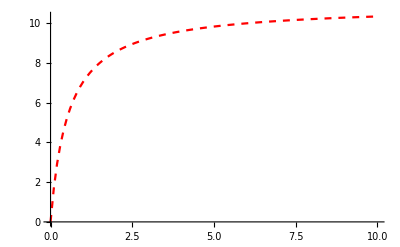

```mathematica
s1=ListPlot[Table[{gamma,-(f2[gamma,0.0001]-f2[gamma,0])10/0.0001},{gamma,0,10,0.1}],Joined->True,PlotRange->All,PlotStyle->{Dashed,Red}]
```

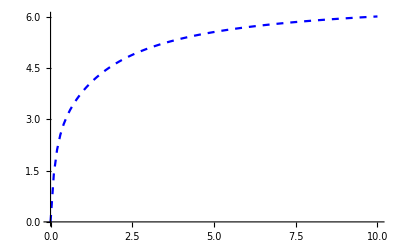

```mathematica
s2=ListPlot[Table[{gamma,(((f2[gamma,0.0002]-f2[gamma,0.0001])/0.0001)-(f2[gamma,0.0001]-f2[gamma,0])/0.0001)10/0.0001},{gamma,0,10,0.1}],Joined->True,PlotStyle->{Dashed,Blue}]
```

```mathematica
ta1=Table[{gamma,-(f2[gamma,0.0001]-f2[gamma,0])10/0.0001},{gamma,0.1,10,0.1}];ta2=Table[{gamma,(((f2[gamma,0.0002]-f2[gamma,0.0001])/0.0001)-(f2[gamma,0.0001]-f2[gamma,0])/0.0001)10/0.0001},{gamma,0.1,10,0.1}];
```

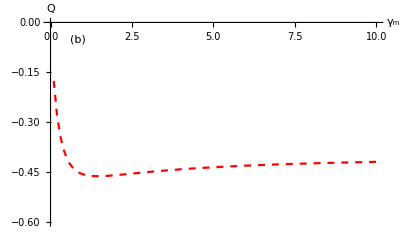

```mathematica
s3=ListPlot[Table[{ta2[[i]][[1]],ta2[[i]][[2]]/ta1[[i]][[2]]-1},{i,1,Length[ta1]}],PlotStyle->{Dashed,Red},Joined->True,PlotRange->{All,{0,-0.6}},PlotStyle->{{Dashed,Blue},{Dashed,Red}},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_m",Italic,24,Black],Style["Q",Italic,24,Black]},PlotRange->All,Epilog->{{Style[Text["(b)",Scaled[{0.1,0.9}]],16,Black]}}]
```

```mathematica
gw=3;gamma=.;g0=4;dt=0.005;Ω=1;ω =0.1;theta=Pi/2;phi=0;oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];t4=Table[{gamma,ct={};ct1={};ct2={};Do[For[n=0,n<2000+1,n++,rho[0]={{(2 g0 gamma (8 gamma gw+gw^2+4 Ω^2) Sin[theta]^2)/(gw (8 gamma+gw) (6 g0 gamma+(g0+gamma) gw)+4 (2 g0 gamma+(g0+gamma) gw) Ω^2+gamma ((2 g0-gw) gw (8 gamma+gw)-4 (2 g0+gw) Ω^2) Cos[2 theta]),0,0},{0,-(2 gamma gw (8 gamma gw+gw^2+4 Ω^2) Sin[theta]^2)/(-gw (8 gamma+gw) (6 g0 gamma+(g0+gamma) gw)-4 (2 g0 gamma+(g0+gamma) gw) Ω^2+gamma (-(2 g0-gw) gw (8 gamma+gw)+4 (2 g0+gw) Ω^2) Cos[2 theta]),0},{0,0,1-(2 g0 gamma (8 gamma gw+gw^2+4 Ω^2) Sin[theta]^2)/(gw (8 gamma+gw) (6 g0 gamma+(g0+gamma) gw)+4 (2 g0 gamma+(g0+gamma) gw) Ω^2+gamma ((2 g0-gw) gw (8 gamma+gw)-4 (2 g0+gw) Ω^2) Cos[2 theta])-(-(2 gamma gw (8 gamma gw+gw^2+4 Ω^2) Sin[theta]^2)/(-gw (8 gamma+gw) (6 g0 gamma+(g0+gamma) gw)-4 (2 g0 gamma+(g0+gamma) gw) Ω^2+gamma (-(2 g0-gw) gw (8 gamma+gw)+4 (2 g0+gw) Ω^2) Cos[2 theta]))}};M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[M0.(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M0]]],1-Chop[Tr[M0.(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M0]]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=Mg0.(M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]/Tr[M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]]).Transpose[Mg0]+Mg1.(M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]/Tr[M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]]).Transpose[Mg1];
];AppendTo[ct,Mean[Table[count[n],{n,0,2000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,2000}]]];AppendTo[ct2,Total[Table[count[n],{n,0,2000}]]];,{5000}];Mean[ct],Mean[ct1],Mean[ct2],Variance[ct2]},{gamma,1,10,1}]
```

{{1,0.00357211,0.00356021,7.1478,3.7151},{2,0.00434903,0.00433106,8.7024,4.87801},{3,0.00468106,0.00466011,9.3668,5.47775},{4,0.00484388,0.00482145,9.6926,5.51521},{5,0.00497581,0.0049521,9.9566,5.71346},{6,0.00508196,0.00505717,10.169,5.97203},{7,0.00514073,0.00511539,10.2866,5.87243},{8,0.00518181,0.005156,10.3688,6.12681},{9,0.0051943,0.00516835,10.3938,6.21636},{10,0.00526427,0.00523763,10.5338,6.1941}}

```mathematica
t4={{1,0.0035721139430284674,0.0035602054972513754,7.1478,3.7150981796359264},{2,0.004349025487256351,0.004331057871064469,8.7024,4.878009841968394},{3,0.004681059470264846,0.004660108245877063,9.3668,5.477753310662133},{4,0.0048438780609694945,0.004821447276361823,9.6926,5.5152082816563315},{5,0.004975812093953001,0.0049521015492253895,9.9566,5.713459131826365},{6,0.005081959020489733,0.0050571688155922065,10.169,5.972033406681337},{7,0.005140729635182386,0.005115392603698153,10.2866,5.872434926985398},{8,0.00518180909545225,0.005156004797601202,10.3688,6.126811922384476},{9,0.005194302848575689,0.005168352723638183,10.3938,6.216364832966594},{10,0.005264267866066943,0.005237626186906551,10.5338,6.194096379275855}};(*This is data saved from one simulation run*)
```

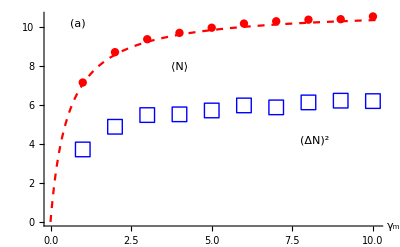

```mathematica
pwa=Show[Plot[(2 g0 gamma (8 gamma gw+gw^2+4 Ω^2) Sin[theta]^2)/(gw (8 gamma+gw) (6 g0 gamma+(g0+gamma) gw)+4 (2 g0 gamma+(g0+gamma) gw) Ω^2+gamma ((2 g0-gw) gw (8 gamma+gw)-4 (2 g0+gw) Ω^2) Cos[2 theta])gw 2000dt,{gamma,0,10.1},PlotStyle->{Red,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_m",Italic,24,Black]},PlotRange->All,Epilog->{{Style[Text["⟨N⟩",Scaled[{0.4,0.75}]],16,Red]},{Style[Text["(a)",Scaled[{0.1,0.95}]],16,Black]},{Style[Text["(ΔN)^2",Scaled[{0.8,0.4}]],16,Blue]}}],ListPlot[Table[{t4[[i]][[1]],t4[[i]][[4]]},{i,1,Length[t4]}],PlotStyle->{Red,PointSize[0.015]}],ListPlot[Table[{t4[[i]][[1]],t4[[i]][[5]]},{i,1,Length[t4]}],PlotRange->All, PlotMarkers->{"□",15},PlotStyle->{Blue}]]
```

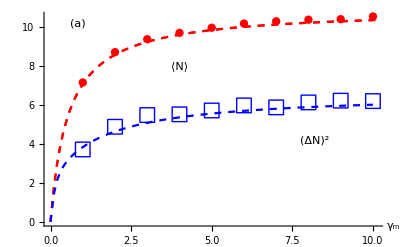

```mathematica
g1=Show[pwa,s1,s2]
```

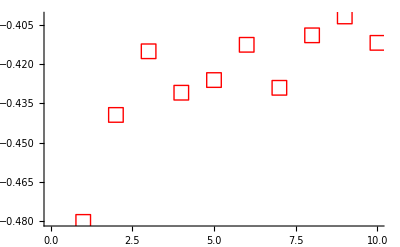

```mathematica
qa2=ListPlot[Table[{t4[[i]][[1]],t4[[i]][[5]]/t4[[i]][[4]]-1},{i,1,Length[t4]}], PlotMarkers->{"□",15},PlotStyle->{Red}]
```

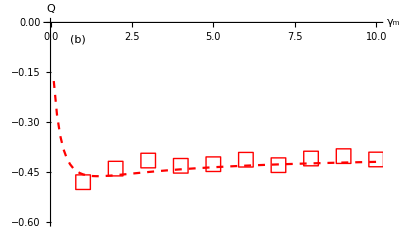

```mathematica
g2=Show[s3,qa2]
```

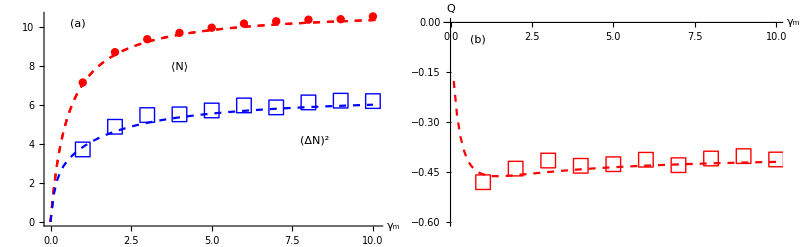

```mathematica
GraphicsGrid[{{g1,g2}},Spacings->{0, 0},ImageSize->800]
```

```mathematica
Clear[H0,r0,Ω ,ω,gamma,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/2;phi=0;gw=3;dt=0.005;gamma=.;gammah=4;gammac=4;
g0=4;betah=(3/Ω);betac=100/ω;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];t5=Table[{gamma,ct={};ct1={};ct2={};Do[For[n=0,n<2000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[(M0.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M0])]],1-Chop[Tr[(M0.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M0])]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])/Tr[(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])];];AppendTo[ct,Mean[Table[count[n],{n,0,2000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,2000}]]];AppendTo[ct2,Total[Table[count[n],{n,0,2000}]]];,{5000}];Mean[ct],Mean[ct1],Mean[ct2],Variance[ct2]},{gamma,1,10,1}]
```

{{1,0.00256682,0.00256061,5.1362,3.59957},{2,0.00347026,0.00345885,6.944,4.39654},{3,0.00394343,0.00392859,7.8908,4.99988},{4,0.00427086,0.0042534,8.546,5.41777},{5,0.00443628,0.00441749,8.877,5.30173},{6,0.00457651,0.0045564,9.1576,5.79792},{7,0.00473263,0.00471121,9.47,5.53861},{8,0.0047931,0.00477105,9.591,5.87289},{9,0.00485297,0.00483042,9.7108,5.6907},{10,0.00495002,0.00492649,9.905,5.96677}}

```mathematica
t5={{1,0.002566816591704136,0.0025606088955522238,5.1362,3.5995694738947783},{2,0.0034702648675662006,0.003458852873563218,6.944,4.396543308661732},{3,0.003943428285857053,0.003928592503748126,7.8908,4.999875335067014},{4,0.004270864567716122,0.004253397101449276,8.546,5.417767553510703},{5,0.0044362818590704435,0.004417485057471266,8.877,5.3017313462692535},{6,0.004576511744127916,0.004556396601699152,9.1576,5.797921824364874},{7,0.004732633683158399,0.004711207296351826,9.47,5.5386077215443095},{8,0.004793103448275841,0.00477104747626187,9.591,5.872893578715742},{9,0.0048529735132433575,0.004830415192403801,9.7108,5.690701500300061},{10,0.004950024987506225,0.004926494352823591,9.905,5.9667683536707345}};(* This is data saved from one simulation run. A redundant Max[0,1-p_tick] command has been removed from prev. version of the code. Different run of the simulation from version 2 of the paper *)
```

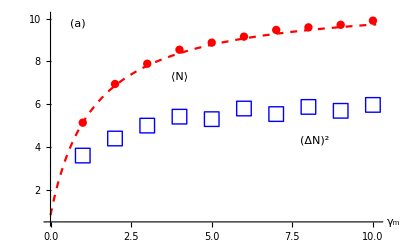

```mathematica
pwwa=Show[Plot[-((ⅇ^(betac ω) gammac (-ⅇ^(2 betac ω) gammah^3-ⅇ^(betac ω+betah Ω) gammah^2 (2 gammac+ⅇ^(betac ω) (13 gamma+2 (gammah+gw)))+ⅇ^(3 betah Ω) gamma (-gammac^2-2 ⅇ^(betac ω) gammac (4 gamma+gammah+gw)-ⅇ^(2 betac ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))+ⅇ^(2 betah Ω) gammah (-gammac^2-2 ⅇ^(betac ω) gammac (7 gamma+gammah+gw)-ⅇ^(2 betac ω) ((4 gamma+gammah+gw) (10 gamma+gammah+gw)+4 Ω^2))+ⅇ^(betah Ω) gamma (ⅇ^(2 betah Ω) gammac^2+2 ⅇ^(betac ω+betah Ω) gammac (-gammah+ⅇ^(betah Ω) (4 gamma+gammah+gw))+ⅇ^(2 betac ω) (-3 gammah^2-2 ⅇ^(betah Ω) gammah (12 gamma+gammah+gw)+ⅇ^(2 betah Ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))) Cos[2 theta]))/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta]))gw 2000dt,{gamma,0,10.1},PlotStyle->{Red,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_m",Italic,24,Black]},PlotRange->{{0,10.1},{0.5,10.1}},Epilog->{{Style[Text["⟨N⟩",Scaled[{0.4,0.7}]],16,Red]},{Style[Text["(a)",Scaled[{0.1,0.95}]],16,Black]},{Style[Text["(ΔN)^2",Scaled[{0.8,0.4}]],16,Blue]}}],ListPlot[Table[{t5[[i]][[1]],t5[[i]][[4]]},{i,1,Length[t5]}],PlotStyle->{Red,PointSize[0.015]}],ListPlot[Table[{t5[[i]][[1]],t5[[i]][[5]]},{i,1,Length[t5]}],PlotRange->All, PlotMarkers->{"□",15},PlotStyle->{Blue}]]
```

## Large deviation calculations

```mathematica
Clear[theta,phi,betah,betac,gamma,gammac,gammah,gw,Ω,ω,dt];phi=0;theta=Pi/2;rhee={{rmm,0,0},{0,rcc,0},{0,0,rgg}};(dt (-I (H0.rhee-rhee.H0)-gamma (oX.(oX.rhee-rhee.oX)-(oX.rhee-rhee.oX).oX)+gammah(Lh.rhee.Lhd-1/2(rhee.Lhd.Lh+Lhd.Lh.rhee))+gammah Exp[-betah Ω ](Lhd.rhee.Lh-1/2(rhee.Lh.Lhd+Lh.Lhd.rhee))+gammac(Lc.rhee.Lcd-1/2(rhee.Lcd.Lc+Lcd.Lc.rhee))+gammac Exp[-betac ω ](Lcd.rhee.Lc-1/2(rhee.Lc.Lcd+Lc.Lcd.rhee))+gw(Exp[-s]Lw.rhee.Lwd-1/2(rhee.Lwd.Lw+Lwd.Lw.rhee))))//FullSimplify
```

{{dt (ⅇ^(-betah Ω) gammah rgg+2 gamma (rgg-rmm)-(gammah+gw) rmm),0,0},{0,dt (-gammac rcc+ⅇ^(-betac ω) gammac rgg+ⅇ^-s gw rmm),0},{0,0,dt (gammac (rcc-ⅇ^(-betac ω) rgg)+2 gamma (-rgg+rmm)+gammah (-ⅇ^(-betah Ω) rgg+rmm))}}

```mathematica
Eqnsa={dt (ⅇ^(-betah Ω) gammah rgg+2 gamma (rgg-rmm)-(gammah+gw) rmm),dt (-gammac rcc+ⅇ^(-betac ω) gammac rgg+ⅇ^-s gw rmm),dt (gammac (rcc-ⅇ^(-betac ω) rgg)+2 gamma (-rgg+rmm)+gammah (-ⅇ^(-betah Ω) rgg+rmm))};
```

```mathematica
ldfnTa=Normal@CoefficientArrays[Eqnsa,{rmm,rcc,rgg}][[2]]/dt//Simplify
```

{{-2 gamma-gammah-gw,0,2 gamma+ⅇ^(-betah Ω) gammah},{ⅇ^-s gw,-gammac,ⅇ^(-betac ω) gammac},{2 gamma+gammah,gammac,-2 gamma-ⅇ^(-betac ω) gammac-ⅇ^(-betah Ω) gammah}}

```mathematica
Eigenvalues[ldfnTa]
```

{ⅇ^(-s-betac ω-betah Ω) Root[-2 ⅇ^(2 s+3 betac ω+3 betah Ω) gamma gammac gw+2 ⅇ^(3 s+3 betac ω+3 betah Ω) gamma gammac gw-ⅇ^(2 s+3 betac ω+2 betah Ω) gammac gammah gw+ⅇ^(3 s+3 betac ω+2 betah Ω) gammac gammah gw+(2 ⅇ^(2 s+betac ω+2 betah Ω) gamma gammac+4 ⅇ^(2 s+2 betac ω+2 betah Ω) gamma gammac+ⅇ^(2 s+2 betac ω+betah Ω) gammac gammah+ⅇ^(2 s+betac ω+2 betah Ω) gammac gammah+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gammah+2 ⅇ^(2 s+2 betac ω+2 betah Ω) gamma gw+ⅇ^(2 s+betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+betah Ω) gammah gw) #1+(4 ⅇ^(s+betac ω+betah Ω) gamma+ⅇ^(s+betah Ω) gammac+ⅇ^(s+betac ω+betah Ω) gammac+ⅇ^(s+betac ω) gammah+ⅇ^(s+betac ω+betah Ω) gammah+ⅇ^(s+betac ω+betah Ω) gw) #1^2+#1^3&,1],ⅇ^(-s-betac ω-betah Ω) Root[-2 ⅇ^(2 s+3 betac ω+3 betah Ω) gamma gammac gw+2 ⅇ^(3 s+3 betac ω+3 betah Ω) gamma gammac gw-ⅇ^(2 s+3 betac ω+2 betah Ω) gammac gammah gw+ⅇ^(3 s+3 betac ω+2 betah Ω) gammac gammah gw+(2 ⅇ^(2 s+betac ω+2 betah Ω) gamma gammac+4 ⅇ^(2 s+2 betac ω+2 betah Ω) gamma gammac+ⅇ^(2 s+2 betac ω+betah Ω) gammac gammah+ⅇ^(2 s+betac ω+2 betah Ω) gammac gammah+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gammah+2 ⅇ^(2 s+2 betac ω+2 betah Ω) gamma gw+ⅇ^(2 s+betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+betah Ω) gammah gw) #1+(4 ⅇ^(s+betac ω+betah Ω) gamma+ⅇ^(s+betah Ω) gammac+ⅇ^(s+betac ω+betah Ω) gammac+ⅇ^(s+betac ω) gammah+ⅇ^(s+betac ω+betah Ω) gammah+ⅇ^(s+betac ω+betah Ω) gw) #1^2+#1^3&,2],ⅇ^(-s-betac ω-betah Ω) Root[-2 ⅇ^(2 s+3 betac ω+3 betah Ω) gamma gammac gw+2 ⅇ^(3 s+3 betac ω+3 betah Ω) gamma gammac gw-ⅇ^(2 s+3 betac ω+2 betah Ω) gammac gammah gw+ⅇ^(3 s+3 betac ω+2 betah Ω) gammac gammah gw+(2 ⅇ^(2 s+betac ω+2 betah Ω) gamma gammac+4 ⅇ^(2 s+2 betac ω+2 betah Ω) gamma gammac+ⅇ^(2 s+2 betac ω+betah Ω) gammac gammah+ⅇ^(2 s+betac ω+2 betah Ω) gammac gammah+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gammah+2 ⅇ^(2 s+2 betac ω+2 betah Ω) gamma gw+ⅇ^(2 s+betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+betah Ω) gammah gw) #1+(4 ⅇ^(s+betac ω+betah Ω) gamma+ⅇ^(s+betah Ω) gammac+ⅇ^(s+betac ω+betah Ω) gammac+ⅇ^(s+betac ω) gammah+ⅇ^(s+betac ω+betah Ω) gammah+ⅇ^(s+betac ω+betah Ω) gw) #1^2+#1^3&,3]}

```mathematica
f3[gamma_,s_]:=Max[Select[Conjugate[Select[{ⅇ^(-s-betac ω-betah Ω) Root[-2 ⅇ^(2 s+3 betac ω+3 betah Ω) gamma gammac gw+2 ⅇ^(3 s+3 betac ω+3 betah Ω) gamma gammac gw-ⅇ^(2 s+3 betac ω+2 betah Ω) gammac gammah gw+ⅇ^(3 s+3 betac ω+2 betah Ω) gammac gammah gw+(2 ⅇ^(2 s+betac ω+2 betah Ω) gamma gammac+4 ⅇ^(2 s+2 betac ω+2 betah Ω) gamma gammac+ⅇ^(2 s+2 betac ω+betah Ω) gammac gammah+ⅇ^(2 s+betac ω+2 betah Ω) gammac gammah+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gammah+2 ⅇ^(2 s+2 betac ω+2 betah Ω) gamma gw+ⅇ^(2 s+betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+betah Ω) gammah gw) #1+(4 ⅇ^(s+betac ω+betah Ω) gamma+ⅇ^(s+betah Ω) gammac+ⅇ^(s+betac ω+betah Ω) gammac+ⅇ^(s+betac ω) gammah+ⅇ^(s+betac ω+betah Ω) gammah+ⅇ^(s+betac ω+betah Ω) gw) #1^2+#1^3&,1],ⅇ^(-s-betac ω-betah Ω) Root[-2 ⅇ^(2 s+3 betac ω+3 betah Ω) gamma gammac gw+2 ⅇ^(3 s+3 betac ω+3 betah Ω) gamma gammac gw-ⅇ^(2 s+3 betac ω+2 betah Ω) gammac gammah gw+ⅇ^(3 s+3 betac ω+2 betah Ω) gammac gammah gw+(2 ⅇ^(2 s+betac ω+2 betah Ω) gamma gammac+4 ⅇ^(2 s+2 betac ω+2 betah Ω) gamma gammac+ⅇ^(2 s+2 betac ω+betah Ω) gammac gammah+ⅇ^(2 s+betac ω+2 betah Ω) gammac gammah+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gammah+2 ⅇ^(2 s+2 betac ω+2 betah Ω) gamma gw+ⅇ^(2 s+betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+betah Ω) gammah gw) #1+(4 ⅇ^(s+betac ω+betah Ω) gamma+ⅇ^(s+betah Ω) gammac+ⅇ^(s+betac ω+betah Ω) gammac+ⅇ^(s+betac ω) gammah+ⅇ^(s+betac ω+betah Ω) gammah+ⅇ^(s+betac ω+betah Ω) gw) #1^2+#1^3&,2],ⅇ^(-s-betac ω-betah Ω) Root[-2 ⅇ^(2 s+3 betac ω+3 betah Ω) gamma gammac gw+2 ⅇ^(3 s+3 betac ω+3 betah Ω) gamma gammac gw-ⅇ^(2 s+3 betac ω+2 betah Ω) gammac gammah gw+ⅇ^(3 s+3 betac ω+2 betah Ω) gammac gammah gw+(2 ⅇ^(2 s+betac ω+2 betah Ω) gamma gammac+4 ⅇ^(2 s+2 betac ω+2 betah Ω) gamma gammac+ⅇ^(2 s+2 betac ω+betah Ω) gammac gammah+ⅇ^(2 s+betac ω+2 betah Ω) gammac gammah+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gammah+2 ⅇ^(2 s+2 betac ω+2 betah Ω) gamma gw+ⅇ^(2 s+betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+betah Ω) gammah gw) #1+(4 ⅇ^(s+betac ω+betah Ω) gamma+ⅇ^(s+betah Ω) gammac+ⅇ^(s+betac ω+betah Ω) gammac+ⅇ^(s+betac ω) gammah+ⅇ^(s+betac ω+betah Ω) gammah+ⅇ^(s+betac ω+betah Ω) gw) #1^2+#1^3&,3]},Im[#]<10^-16&]],Im[#]<10^-16&]]
```

```mathematica
Ω =1;ω =0.1;theta=Pi/2;phi=0;gw=3;dt=0.01;gamma=.;gammah=4;gammac=4;
g0=4;betah=(3/Ω);betac=100/ω;
```

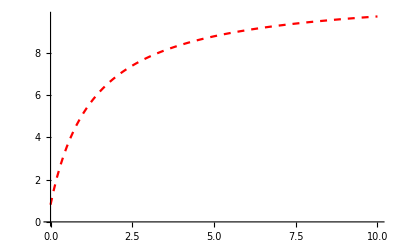

```mathematica
ss1=ListPlot[Table[{gamma,-(f3[gamma,0.00001]-f3[gamma,0])10/0.00001},{gamma,0,10,0.1}],Joined->True,PlotRange->All,PlotStyle->{Dashed,Red}]
```

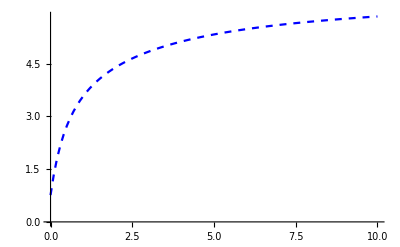

```mathematica
ss2=ListPlot[Table[{gamma,(((f3[gamma,0.0002]-f3[gamma,0.0001])/0.0001)-(f3[gamma,0.0001]-f3[gamma,0])/0.0001)10/0.0001},{gamma,0,10,0.1}],Joined->True,PlotStyle->{Dashed,Blue}]
```

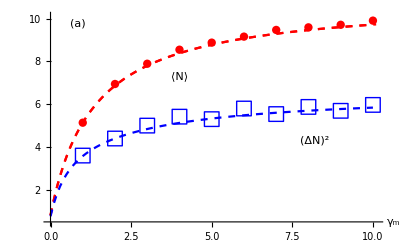

```mathematica
gg1=Show[pwwa,ss1,ss2]
```

```mathematica
taa1=Table[{gamma,-(f3[gamma,0.0001]-f3[gamma,0])10/0.0001},{gamma,0.1,10,0.1}];taa2=Table[{gamma,(((f3[gamma,0.0002]-f3[gamma,0.0001])/0.0001)-(f3[gamma,0.0001]-f3[gamma,0])/0.0001)10/0.0001},{gamma,0.1,10,0.1}];
```

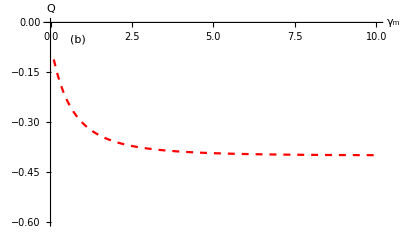

```mathematica
ss3=ListPlot[Table[{taa2[[i]][[1]],taa2[[i]][[2]]/taa1[[i]][[2]]-1},{i,1,Length[taa1]}],PlotStyle->{Dashed,Red},Joined->True,PlotRange->{All,{0,-0.6}},PlotStyle->{{Dashed,Blue},{Dashed,Red}},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_m",Italic,24,Black],Style["Q",Italic,24,Black]},PlotRange->All,Epilog->{{Style[Text["(b)",Scaled[{0.1,0.9}]],16,Black]}}]
```

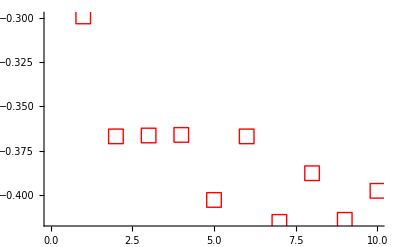

```mathematica
qaa2=ListPlot[Table[{t5[[i]][[1]],t5[[i]][[5]]/t5[[i]][[4]]-1},{i,1,Length[t5]}], PlotMarkers->{"□",15},PlotStyle->{Red}]
```

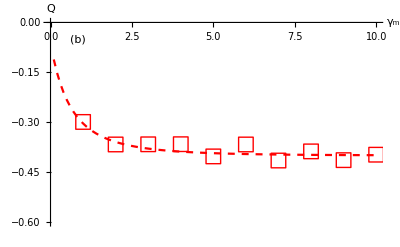

```mathematica
gg2=Show[ss3,qaa2]
```

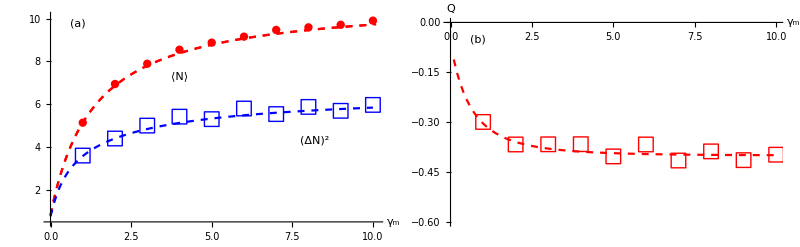

```mathematica
GraphicsGrid[{{gg1,gg2}},Spacings->{0, 0},ImageSize->800]
```

## Purely thermal example

```mathematica
Clear[H0,r0,Ω ,ω,gamma,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=0;phi=0;gw=3;dt=0.01;gamma=0;gammah=.;gammac=4;
g0=4;betah=(3/Ω);betac=100/ω;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];t6=Table[{gammah,ct={};ct1={};ct2={};Do[For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[(M0.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M0])]],1-Chop[Tr[(M0.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M0])]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])/Tr[(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])];];AppendTo[ct,Mean[Table[count[n],{n,0,1000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,1000}]]];AppendTo[ct2,Total[Table[count[n],{n,0,1000}]]];,{5000}];Mean[ct],Mean[ct1],Mean[ct2],Variance[ct2]},{gammah,1,10,1}]
```

```mathematica
t6={{1,0.0003588411588411583,0.00035873246753246696,0.3592,0.3390431686337268},{2,0.0005826173826173811,0.0005823116883116871,0.5832,0.5491875975195039},{3,0.0007102897102897084,0.0007098093906093892,0.711,0.6864162832566513},{4,0.0008235764235764219,0.0008229422577422565,0.8244,0.7797205841168234},{5,0.0009062937062937049,0.000905537262737262,0.9072,0.8415564712942587},{6,0.0009602397602397595,0.0009593570429570425,0.9612,0.921078775755151},{7,0.0009958041958041952,0.000994873926073926,0.9968,0.934576675335067},{8,0.0010249750249750242,0.0010240079920079918,1.026,0.9415123024604922},{9,0.0010747252747252745,0.0010736307692307695,1.0758,1.0142572114422885},{10,0.001092107892107892,0.0010909782217782221,1.0932,1.0291195839167835}};
```

```mathematica
(*This is data saved from one simulation run. A redundant Max[0,1-p_tick] command has been removed from prev. version of the code *)
```

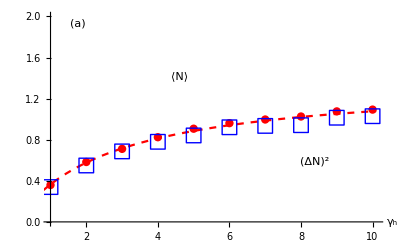

```mathematica
pka=Show[Plot[-((ⅇ^(betac ω) gammac (-ⅇ^(2 betac ω) gammah^3-ⅇ^(betac ω+betah Ω) gammah^2 (2 gammac+ⅇ^(betac ω) (13 gamma+2 (gammah+gw)))+ⅇ^(3 betah Ω) gamma (-gammac^2-2 ⅇ^(betac ω) gammac (4 gamma+gammah+gw)-ⅇ^(2 betac ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))+ⅇ^(2 betah Ω) gammah (-gammac^2-2 ⅇ^(betac ω) gammac (7 gamma+gammah+gw)-ⅇ^(2 betac ω) ((4 gamma+gammah+gw) (10 gamma+gammah+gw)+4 Ω^2))+ⅇ^(betah Ω) gamma (ⅇ^(2 betah Ω) gammac^2+2 ⅇ^(betac ω+betah Ω) gammac (-gammah+ⅇ^(betah Ω) (4 gamma+gammah+gw))+ⅇ^(2 betac ω) (-3 gammah^2-2 ⅇ^(betah Ω) gammah (12 gamma+gammah+gw)+ⅇ^(2 betah Ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))) Cos[2 theta]))/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta]))gw 1000dt,{gammah,0,10.1},PlotStyle->{Red,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_h",Italic,24,Black]},PlotRange->{{1,10.1},{0,2}},Epilog->{{Style[Text["⟨N⟩",Scaled[{0.4,0.7}]],16,Red]},{Style[Text["(a)",Scaled[{0.1,0.95}]],16,Black]},{Style[Text["(ΔN)^2",Scaled[{0.8,0.3}]],16,Blue]}}],ListPlot[Table[{t6[[i]][[1]],t6[[i]][[4]]},{i,1,Length[t6]}],PlotStyle->{Red,PointSize[0.015]}],ListPlot[Table[{t6[[i]][[1]],t6[[i]][[5]]},{i,1,Length[t6]}],PlotRange->All, PlotMarkers->{"□",15},PlotStyle->{Blue}]]
```

```mathematica
Clear[theta,phi,betah,betac,gamma,gammac,gammah,gw,Ω,ω];gamma=0;
```

```mathematica
rhee={{rmm,0,0},{0,rcc,0},{0,0,rgg}};(dt (-I (H0.rhee-rhee.H0)-gamma (oX.(oX.rhee-rhee.oX)-(oX.rhee-rhee.oX).oX)+gammah(Lh.rhee.Lhd-1/2(rhee.Lhd.Lh+Lhd.Lh.rhee))+gammah Exp[-betah Ω ](Lhd.rhee.Lh-1/2(rhee.Lh.Lhd+Lh.Lhd.rhee))+gammac(Lc.rhee.Lcd-1/2(rhee.Lcd.Lc+Lcd.Lc.rhee))+gammac Exp[-betac ω ](Lcd.rhee.Lc-1/2(rhee.Lc.Lcd+Lc.Lcd.rhee))+gw(Exp[-s]Lw.rhee.Lwd-1/2(rhee.Lwd.Lw+Lwd.Lw.rhee))))//FullSimplify
```

{{0.01 ⅇ^(-betah Ω) gammah rgg-0.01 gammah rmm-0.01 gw rmm,0.,0.},{0.,0.01 (-gammac rcc+ⅇ^(-betac ω) gammac rgg+ⅇ^-s gw rmm),0.},{0.,0.,0.01 (gammac (rcc-ⅇ^(-betac ω) rgg)+gammah (-ⅇ^(-betah Ω) rgg+rmm))}}

```mathematica
Eas={dt (ⅇ^(-betah Ω) gammah rgg-(gammah+gw) rmm),dt (-gammac rcc+ⅇ^(-betac ω) gammac rgg+ⅇ^-s gw rmm),dt (gammac (rcc-ⅇ^(-betac ω) rgg)+gammah (-ⅇ^(-betah Ω) rgg+rmm))};
```

```mathematica
ldfnT=Normal@CoefficientArrays[Eas,{rmm,rcc,rgg}][[2]]/dt//Simplify
```

{{-1. (gammah+gw),0.,1. ⅇ^(-1. betah Ω) gammah},{1. ⅇ^(-1. s) gw,-1. gammac,1. ⅇ^(-1. betac ω) gammac},{1. gammah,1. gammac,-1. ⅇ^(-1. betac ω) gammac-1. ⅇ^(-1. betah Ω) gammah}}

```mathematica
Eigenvalues[ldfnT]
```

{1. ⅇ^(-1. s-1. betac ω-1. betah Ω) Root[-1. ⅇ^(2. s+3. betac ω+2. betah Ω) gammac gammah gw+1. ⅇ^(3. s+3. betac ω+2. betah Ω) gammac gammah gw+(1. ⅇ^(2. s+2. betac ω+1. betah Ω) gammac gammah+1. ⅇ^(2. s+1. betac ω+2. betah Ω) gammac gammah+1. ⅇ^(2. s+2. betac ω+2. betah Ω) gammac gammah+1. ⅇ^(2. s+1. betac ω+2. betah Ω) gammac gw+1. ⅇ^(2. s+2. betac ω+2. betah Ω) gammac gw+1. ⅇ^(2. s+2. betac ω+1. betah Ω) gammah gw) #1+(1. ⅇ^(1. s+1. betah Ω) gammac+1. ⅇ^(1. s+1. betac ω+1. betah Ω) gammac+1. ⅇ^(1. s+1. betac ω) gammah+1. ⅇ^(1. s+1. betac ω+1. betah Ω) gammah+1. ⅇ^(1. s+1. betac ω+1. betah Ω) gw) #1^2+1. #1^3&,1],1. ⅇ^(-1. s-1. betac ω-1. betah Ω) Root[-1. ⅇ^(2. s+3. betac ω+2. betah Ω) gammac gammah gw+1. ⅇ^(3. s+3. betac ω+2. betah Ω) gammac gammah gw+(1. ⅇ^(2. s+2. betac ω+1. betah Ω) gammac gammah+1. ⅇ^(2. s+1. betac ω+2. betah Ω) gammac gammah+1. ⅇ^(2. s+2. betac ω+2. betah Ω) gammac gammah+1. ⅇ^(2. s+1. betac ω+2. betah Ω) gammac gw+1. ⅇ^(2. s+2. betac ω+2. betah Ω) gammac gw+1. ⅇ^(2. s+2. betac ω+1. betah Ω) gammah gw) #1+(1. ⅇ^(1. s+1. betah Ω) gammac+1. ⅇ^(1. s+1. betac ω+1. betah Ω) gammac+1. ⅇ^(1. s+1. betac ω) gammah+1. ⅇ^(1. s+1. betac ω+1. betah Ω) gammah+1. ⅇ^(1. s+1. betac ω+1. betah Ω) gw) #1^2+1. #1^3&,2],1. ⅇ^(-1. s-1. betac ω-1. betah Ω) Root[-1. ⅇ^(2. s+3. betac ω+2. betah Ω) gammac gammah gw+1. ⅇ^(3. s+3. betac ω+2. betah Ω) gammac gammah gw+(1. ⅇ^(2. s+2. betac ω+1. betah Ω) gammac gammah+1. ⅇ^(2. s+1. betac ω+2. betah Ω) gammac gammah+1. ⅇ^(2. s+2. betac ω+2. betah Ω) gammac gammah+1. ⅇ^(2. s+1. betac ω+2. betah Ω) gammac gw+1. ⅇ^(2. s+2. betac ω+2. betah Ω) gammac gw+1. ⅇ^(2. s+2. betac ω+1. betah Ω) gammah gw) #1+(1. ⅇ^(1. s+1. betah Ω) gammac+1. ⅇ^(1. s+1. betac ω+1. betah Ω) gammac+1. ⅇ^(1. s+1. betac ω) gammah+1. ⅇ^(1. s+1. betac ω+1. betah Ω) gammah+1. ⅇ^(1. s+1. betac ω+1. betah Ω) gw) #1^2+1. #1^3&,3]}

```mathematica
EVF={ⅇ^(-s-betac ω-betah Ω) Root[-ⅇ^(2 s+3 betac ω+2 betah Ω) gammac gammah gw+ⅇ^(3 s+3 betac ω+2 betah Ω) gammac gammah gw+(ⅇ^(2 s+2 betac ω+betah Ω) gammac gammah+ⅇ^(2 s+betac ω+2 betah Ω) gammac gammah+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gammah+ⅇ^(2 s+betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+betah Ω) gammah gw) #1+(ⅇ^(s+betah Ω) gammac+ⅇ^(s+betac ω+betah Ω) gammac+ⅇ^(s+betac ω) gammah+ⅇ^(s+betac ω+betah Ω) gammah+ⅇ^(s+betac ω+betah Ω) gw) #1^2+#1^3&,1],ⅇ^(-s-betac ω-betah Ω) Root[-ⅇ^(2 s+3 betac ω+2 betah Ω) gammac gammah gw+ⅇ^(3 s+3 betac ω+2 betah Ω) gammac gammah gw+(ⅇ^(2 s+2 betac ω+betah Ω) gammac gammah+ⅇ^(2 s+betac ω+2 betah Ω) gammac gammah+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gammah+ⅇ^(2 s+betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+betah Ω) gammah gw) #1+(ⅇ^(s+betah Ω) gammac+ⅇ^(s+betac ω+betah Ω) gammac+ⅇ^(s+betac ω) gammah+ⅇ^(s+betac ω+betah Ω) gammah+ⅇ^(s+betac ω+betah Ω) gw) #1^2+#1^3&,2],ⅇ^(-s-betac ω-betah Ω) Root[-ⅇ^(2 s+3 betac ω+2 betah Ω) gammac gammah gw+ⅇ^(3 s+3 betac ω+2 betah Ω) gammac gammah gw+(ⅇ^(2 s+2 betac ω+betah Ω) gammac gammah+ⅇ^(2 s+betac ω+2 betah Ω) gammac gammah+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gammah+ⅇ^(2 s+betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+betah Ω) gammah gw) #1+(ⅇ^(s+betah Ω) gammac+ⅇ^(s+betac ω+betah Ω) gammac+ⅇ^(s+betac ω) gammah+ⅇ^(s+betac ω+betah Ω) gammah+ⅇ^(s+betac ω+betah Ω) gw) #1^2+#1^3&,3]};
```

```mathematica
Ω =1;ω =0.1;theta=0;phi=0;gw=3;dt=0.01;gamma=0;gammah=.;gammac=4;
g0=4;betah=(3/Ω);betac=100/ω;
```

```mathematica
f4[gammah_,s_]:=Max[Select[Conjugate[Select[{ⅇ^(-s-betac ω-betah Ω) Root[-ⅇ^(2 s+3 betac ω+2 betah Ω) gammac gammah gw+ⅇ^(3 s+3 betac ω+2 betah Ω) gammac gammah gw+(ⅇ^(2 s+2 betac ω+betah Ω) gammac gammah+ⅇ^(2 s+betac ω+2 betah Ω) gammac gammah+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gammah+ⅇ^(2 s+betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+betah Ω) gammah gw) #1+(ⅇ^(s+betah Ω) gammac+ⅇ^(s+betac ω+betah Ω) gammac+ⅇ^(s+betac ω) gammah+ⅇ^(s+betac ω+betah Ω) gammah+ⅇ^(s+betac ω+betah Ω) gw) #1^2+#1^3&,1],ⅇ^(-s-betac ω-betah Ω) Root[-ⅇ^(2 s+3 betac ω+2 betah Ω) gammac gammah gw+ⅇ^(3 s+3 betac ω+2 betah Ω) gammac gammah gw+(ⅇ^(2 s+2 betac ω+betah Ω) gammac gammah+ⅇ^(2 s+betac ω+2 betah Ω) gammac gammah+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gammah+ⅇ^(2 s+betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+betah Ω) gammah gw) #1+(ⅇ^(s+betah Ω) gammac+ⅇ^(s+betac ω+betah Ω) gammac+ⅇ^(s+betac ω) gammah+ⅇ^(s+betac ω+betah Ω) gammah+ⅇ^(s+betac ω+betah Ω) gw) #1^2+#1^3&,2],ⅇ^(-s-betac ω-betah Ω) Root[-ⅇ^(2 s+3 betac ω+2 betah Ω) gammac gammah gw+ⅇ^(3 s+3 betac ω+2 betah Ω) gammac gammah gw+(ⅇ^(2 s+2 betac ω+betah Ω) gammac gammah+ⅇ^(2 s+betac ω+2 betah Ω) gammac gammah+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gammah+ⅇ^(2 s+betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+2 betah Ω) gammac gw+ⅇ^(2 s+2 betac ω+betah Ω) gammah gw) #1+(ⅇ^(s+betah Ω) gammac+ⅇ^(s+betac ω+betah Ω) gammac+ⅇ^(s+betac ω) gammah+ⅇ^(s+betac ω+betah Ω) gammah+ⅇ^(s+betac ω+betah Ω) gw) #1^2+#1^3&,3]},Im[#]<10^-16&]],Im[#]<10^-16&]]
```

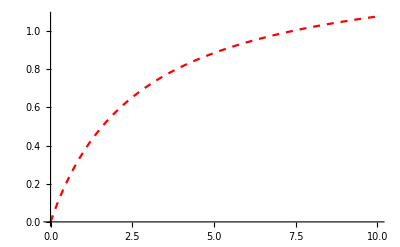

```mathematica
sk1=ListPlot[Table[{gammah,-(f4[gammah,0.00001]-f4[gammah,0])10/0.00001},{gammah,0,10,0.1}],Joined->True,PlotRange->All,PlotStyle->{Dashed,Red}]
```

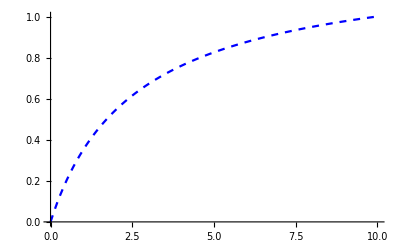

```mathematica
sk2=ListPlot[Table[{gamma,(((f4[gamma,0.0002]-f4[gamma,0.0001])/0.0001)-(f4[gamma,0.0001]-f4[gamma,0])/0.0001)10/0.0001},{gamma,0,10,0.1}],Joined->True,PlotStyle->{Dashed,Blue}]
```

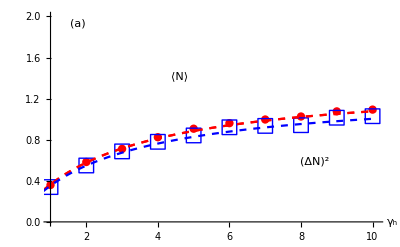

```mathematica
d1=Show[pka,sk1,sk2]
```

```mathematica
tk1=Table[{gammah,-(f4[gammah,0.0001]-f4[gammah,0])10/0.0001},{gammah,0.1,10,0.1}];tk2=Table[{gammah,(((f4[gammah,0.0002]-f4[gammah,0.0001])/0.0001)-(f4[gammah,0.0001]-f4[gammah,0])/0.0001)10/0.0001},{gammah,0.1,10,0.1}];
```

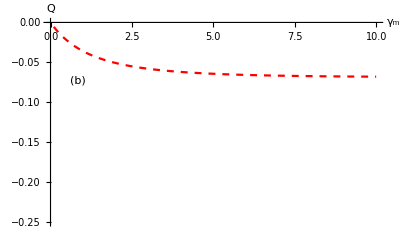

```mathematica
sk3=ListPlot[Table[{tk2[[i]][[1]],tk2[[i]][[2]]/tk1[[i]][[2]]-1},{i,1,Length[tk1]}],PlotStyle->{Dashed,Red},Joined->True,PlotRange->{All,{0,-0.25}},PlotStyle->{{Dashed,Blue},{Dashed,Red}},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_m",Italic,24,Black],Style["Q",Italic,24,Black]},PlotRange->All,Epilog->{{Style[Text["(b)",Scaled[{0.1,0.7}]],16,Black]}}]
```

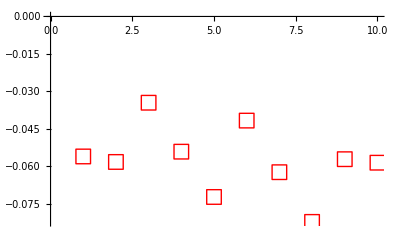

```mathematica
qk3=ListPlot[Table[{t6[[i]][[1]],t6[[i]][[5]]/t6[[i]][[4]]-1},{i,1,Length[t6]}], PlotMarkers->{"□",15},PlotStyle->{Red}]
```

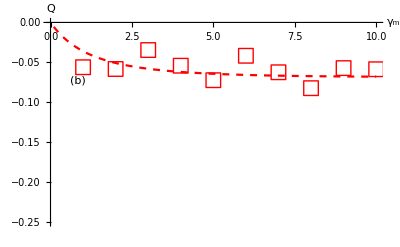

```mathematica
Show[sk3,qk3]
```